# Superconducting qubits Hub

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

```mathematica
(* Subscript[ρ, ∞]=p|0X0|+(1-p)|1X1| *)
Subscript[gAmp, q_][γ_,p_]:=Subscript[Kraus, q][{
	Sqrt[p]*{{1,0},{0,Sqrt[1-γ]}},
	Sqrt[p]*{{0,Sqrt[γ]},{0,0}},
	Sequence@@If[p<1, 
	{Sqrt[1-p]*{{Sqrt[1-γ],0},{0,1}},
	Sqrt[1-p]*{{0,0},{Sqrt[γ],0}}},{}]}]
```

```mathematica
ρ=CreateDensityQureg[6];
```

```mathematica
(* excited state population in percent *)
excp={3.2,2.1,0.8,0.9,2.5,0.7};
```

```mathematica
(* probability of output zero *)
initp0=1-0.01*excp
```

{0.968,0.979,0.992,0.991,0.975,0.993}

```mathematica
initmat=KroneckerProduct@@({{#,0},{0,1-#}}&/@initp0);
```

```mathematica
(*** fid: (Tr[Sqrt[ρσ]])^2  ***)
fidDM::usage="fidDM[ρ,σ], ρ=qureq, sσ=square root of density matrix. Fidelity of two density matrices.";
fidDM[ρ_,σ_]:=Re[Tr[MatrixPower[GetQuregMatrix[ρ].σ,1/2]]^2]
```

```mathematica
(* initialise matrix as a random mix state *)
SetQuregMatrix[ρ,RandomMixState[6]];
t1=20;
t2=30;

δt=1;
data=Table[
t1decay=Subscript[gAmp, #-1][(1-ⅇ^(-δt/t1)),initp0[[#]]]&/@Range[6];
t2decay=Subscript[Deph, #][(1-ⅇ^(-δt/t2))0.5]&/@Range[0,5];
ApplyCircuit[ρ,Join[t1decay,t2decay]];
{t,fidDM[ρ,initmat]}
,{t,δt,120,δt}];
```

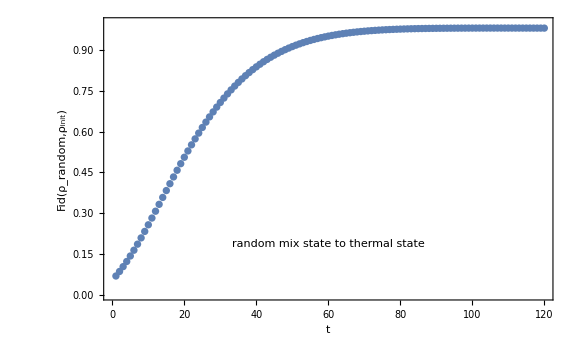

```mathematica
ListPlot[data,PlotRange->{Automatic,{0,1}},Frame->True,FrameLabel->{"t","Fid(ρ_random,ρ_init)"},FrameStyle->Directive[Black,Thick],ImageSize->Large,BaseStyle->{17},Epilog->Inset["random mix state to thermal state",Scaled[{0.5,0.2}]]]
```

```mathematica
(* T1 experiment *)
t1=20;
t2=30;
δt=0.5;
dataT1=Table[
ApplyCircuit[InitZeroState@ρ,Subscript[X, #]&/@Range[0,5]];
t1decay=Subscript[gAmp, #-1][(1-ⅇ^(-t/t1)),initp0[[#]]]&/@Range[6];
t2decay=Subscript[Deph, #][(1-ⅇ^(-t/t2))0.5]&/@Range[0,5];
ApplyCircuit[ρ,Join[t1decay,t2decay]];
{t,CalcProbOfOutcome[ρ,#,1]}&/@Range[0,5]
,{t,0,120,δt}];
```

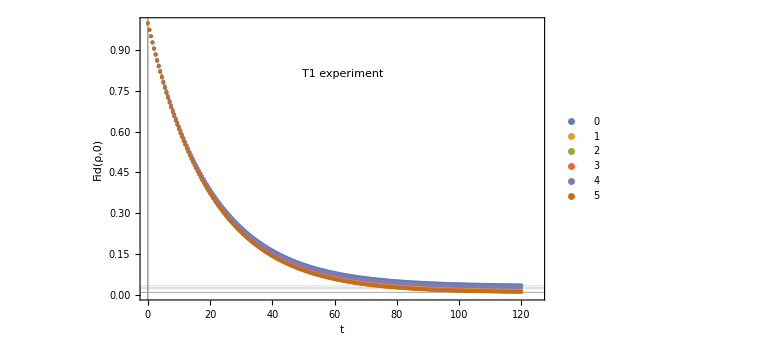

```mathematica
ListPlot[Transpose[dataT1],Frame->True,PlotLegends->Range[0,5],GridLines->{excp*0.01},PlotRange->{{0,125},{0,1}},Frame->True,FrameLabel->{"t","Fid(ρ,0)"},FrameStyle->Directive[Black,Thick],ImageSize->Large,BaseStyle->{17},Epilog->Inset["T1 experiment",Scaled[{0.5,0.8}]]]
```

```mathematica
(* T2 experiment *)
t1=20;
t2=30;
δt=1;
dataT2=Table[
ApplyCircuit[InitZeroState@ρ,Subscript[H, #]&/@Range[0,5]];
t1decay=Subscript[gAmp, #-1][(1-ⅇ^(-t/t1)),initp0[[#]]]&/@Range[6];
t2decay=Subscript[Deph, #][(1-ⅇ^(-t/t2))0.5]&/@Range[0,5];
ApplyCircuit[ρ,Join[t1decay,t2decay]];

ApplyCircuit[ρ,Subscript[H, #]&/@Range[0,5]];
{t,CalcProbOfOutcome[ρ,#,0]}&/@Range[0,5]
,{t,0,120,δt}];
```

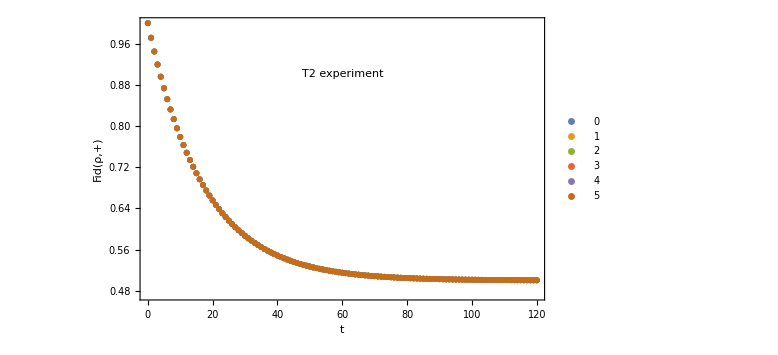

```mathematica
ListPlot[Transpose[dataT2],PlotLegends->Placed[Range[0,5],{0.9,0.5}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thick],ImageSize->Large,FrameLabel->{"t","Fid(ρ,+)"},BaseStyle->{17},Epilog->Inset["T2 experiment",Scaled[{0.5,0.8}]]]
```